# Thesis Notebook

## 2D Orbit with the Tolman VII neutron star density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = 8;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### Coord transforms

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2; 

rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

### Lapse and shift

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

```mathematica
rbarStar = rbarofrOutside[RStar] //  N
```

6.9641

## Tolman VII Isotropic coords definitions

### Constants

```mathematica
rho0 = (15M)/(8 Pi RStar^3);
```

```mathematica
ScriptC = (8 Pi)/15 RStar^2 rho0;
```

### Universal alpha factor

```mathematica
(*alpha:=a0+a1*(Cn/(rhoc*R^2))+a2*(Cn/(rhoc*R^2))^2*)
alpha=3.70625 -1.50266*(ScriptC^(.903)/(rho0*RStar^2))+0.0643875*(ScriptC^(.903)/(rho0*RStar^2))^2 ;
(*alpha = 1*)
```

### New interior rho

```mathematica
rho[r_] := rho0(1 - alpha (r/RStar)^2 + (alpha-1)(r/RStar)^4)
```

### New mass function

```mathematica
MassFunc[r_] := Piecewise[
{
{4 Pi rho0 RStar^3 ( 1/3(r/RStar)^3 - alpha/5(r/RStar)^5 + ((alpha-1)/7)(r/RStar)^7), r < RStar},
{M, r >= RStar}
}
]
```

### Need old grr to use improved model

```mathematica
grrTol[r_] := 1 - (8 Pi)/15 RStar^2 rho0 (r/RStar)^2(5 - 3(r/RStar)^2)
grrTol[RStar] (*Matches with Schw exterior*)
```

3/4

### Constants of integration

```mathematica
C1Imp = (1 - 2ScriptC)(1 + (8 Pi RStar^2 rho0 (10 - 3 alpha)^2(15 - 16 Pi RStar^2 rho0))/(3(105 + 16 Pi RStar^2 rho0(3 alpha-10))^2));

C2Imp = ArcTan[-(2(10 - 3alpha)RStar Sqrt[6 Pi rho0 (15 - 16 Pi rho0 RStar^2)])/(48 Pi (10 - 3 alpha)rho0 RStar^2-315)] + 1/2 Log[1/6 + Sqrt[5/(8 Pi rho0 RStar^2) - 2/3]];
```

### “Phi” improved

```mathematica
PhiImp[r_] := C2Imp - 1/2 Log[(r/RStar)^2 - 5/6 + Sqrt[5 grrTol[r]/(8 Pi RStar^2 rho0)]]
```

### gtt component

```mathematica
gttImp[r_] := 1.1547005383792517 C1Imp (Cos[PhiImp[r]])^2
```

```mathematica
gttImp[RStar] (*<Matches with Schw exterior*)
```

0.866025

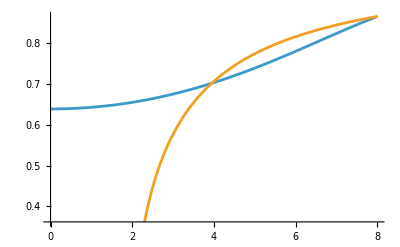

```mathematica
Plot[{gttImp[r], α[rbarofrOutside[r]]}, {r, 0, RStar}]
```

### Pressure

```mathematica
Pressure[r_] := Sqrt[(grrTol[r] rho0)/(10 Pi)](Tan[PhiImp[r]]/RStar) + 1/15(3 (r/RStar)^2 - 5)rho0
```

```mathematica
Pressure[RStar]
```

9.33774×10^-6

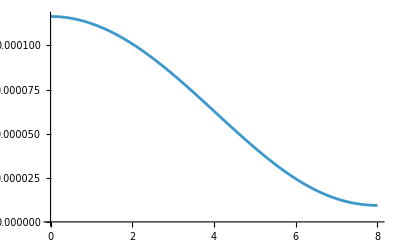

```mathematica
Plot[Pressure[r], {r, 0, RStar}]
```

#### Solving for the new r̄(r) and r(r̄) inside, obtaining r(r̄) via the interpolation trick Sarp explained

```mathematica
(*Defining the ODE*)
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
```

```mathematica
rmin = 10^-16;
```

Numerically Integrating the above equation.

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, RStar, rmin}
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

```mathematica
rbarofrInside[RStar]
rbarofrOutside[RStar] //N
```

6.9641

6.9641

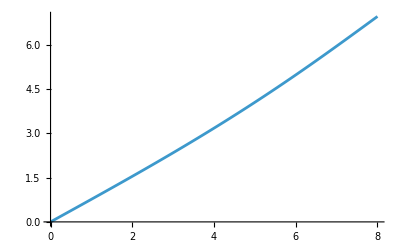

```mathematica
Plot[rbarofrInside[r], {r, 0, RStar}]
```

Now using the interpolation trick to obtain r(r̄):

```mathematica
(*Generating the numerical data points:*)
(*Table[ expression, {variable, start, end, step}*)
data = Prepend[Table[
{rbarofrInside[r], r}, (*Here Mathematica stores rbar[r] and r as a 2 element list - first entry is the independent variable and the one after is the dependent variable*)
{r, rmin, RStar, (RStar - rmin)/100000} (*100000 points*)
], {0,0}];
```

```mathematica
(*Evaluates ok at zero as sarp mentioned but integral doesn't like it one bit*)
```

```mathematica
(*Inverse Interpolation*)
rofrbarInside = Interpolation[data];(*Builds a function from the data passing through all points unlike Fit which approximately matches the data to a function I give it with parameters,  FindFit finds the parameters for me given I guess a suitable function*)
```

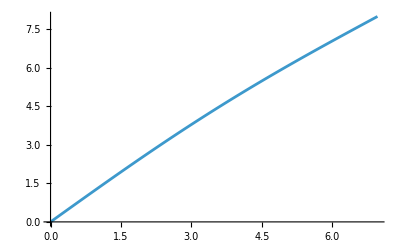

```mathematica
Plot[rofrbarInside[rbar], {rbar, 0, rbarStar}]
```

```mathematica
rofrbarInside[0];
```

#### Writing clean full r(r̄) equation to try and rid discontinuities

```mathematica
rofrbarFull[rbar_?NumericQ] := Piecewise[
{
{rofrbarInside[rbar], rbar < rbarStar},
{rofrbarOutside[rbar], rbar >= rbarStar}
}
];
```

### Putting this together to find the new interior metric functions in isotropic coords

#### Alpha

```mathematica
C1Imp
```

0.796824

```mathematica
αInside[rbar_] := 1.1547005383792517 C1Imp(Cos[PhiImp[rofrbarInside[rbar]]])^2
```

```mathematica
αInside[rbarStar]
```

0.866025

```mathematica
α[rbarStar]
```

0.866025

```mathematica
0.8660254037844388/(0.9412371459117921*0.7968236307476608)
```

1.1547

```mathematica
DERαInside[rbar_] := Derivative[1][gttImp][r] /. r-> rofrbarInside[rbar];
```

```mathematica
DERαInside[rbarStar]
DERαOutside[rbarStar]
```

0.0382523

0.0180422

#### A Inside

```mathematica
AInside[rbar_] := rofrbarInside[rbar]/rbar;
```

```mathematica
AInside[rbarStar]
A[rbarStar]
```

1.14875

1.14875

#### finding alpha in terms of normal r first

Exterior alpha derivative

```mathematica
DERαOutsiderbardummy = Derivative[1][α][rbar];
DERαOutsiderbar[r_] := ((1-1/(2 rbar))/(2 (1+1/(2 rbar))^2 rbar^2)+1/(2 (1+1/(2 rbar)) rbar^2) )/. rbar -> rbarofrOutside[r] (*More accurate subbing in after for rbar maybe?*)
drbardr[r_] := rbarofrOutside[r]/r(1 - (2MassFunc[r])/r)^(-1/2)
```

```mathematica
DERalpha[r_] := drbardr[r]  DERαOutsiderbar[r]
```

```mathematica
DERalpha[RStar] //N
```

0.0180422

```mathematica
DERalpha[rbarofrOutside[RStar]] //N
```

0.0241082

```mathematica
DERαOutside[rbar_] := drbardr[rofrbarOutside[rbar]]  DERαOutsiderbar[rofrbarOutside[rbar]]
```

```mathematica
DERαInside[rbarStar]
```

0.0331275

```mathematica
DERαOutside[rbarStar]
```

0.0180422

```mathematica
(*DERαFull[rbar_]:=If[rbar<rbarStar,DERαInside[rbar],DERαOutside[rbar]]*)
```

Going to do the same derivative setup as the α component for the A component

```mathematica
AInside[rbar_?NumericQ] := rofrbarInside[rbar]/rbar;
```

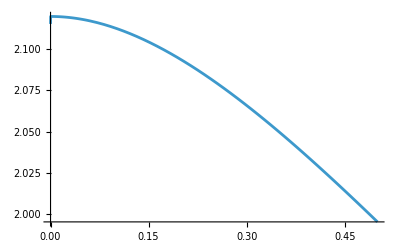

```mathematica
Plot[AInside[rbar], {rbar, 0, .5}]
```

```mathematica
A[rbarStar]
AInside[rbarStar]
```

1.14875

1.14875

```mathematica
AFull[rbar_] := Piecewise[
{
{A[rbar], rbar >= rbarStar},
{AInside[rbar], rbar < rbarStar}
}
];
(*AFull[rbar_]:=If[rbar<rbarStar,AInside[rbar],A[rbar]]*)
```

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
drdrbar[rbar_] := rofrbarInside[rbar]/rbar(1 - (2MassFunc[rofrbarInside[rbar]])/rofrbarInside[rbar])^(1/2)
```

```mathematica
DERAInside[rbar_] := drdrbar[rbar]/rbar - rofrbarInside[rbar]/rbar^2;
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

```mathematica
DERAFull[rbar_] := Piecewise[
{
{DERAOutside[rbar], rbar >=rbarStar},
{DERAInside[rbar], rbar < rbarStar}
}
];
(*DERAFull[rbar_]:=If[rbar<rbarStar,DERAInside[rbar],DERAOutside[rbar]]*)
```

```mathematica
DERAOutside[rbarStar]
DERAInside[rbarStar]
```

-0.0220995

-0.0220995

#### Density and Pressure in isotropic coordinates

```mathematica
rho0 = rhoCentre[RStar];
```

```mathematica
rho[rbar_] :=Piecewise[
{
{rho0(1 - rofrbarInside[rbar]/RStar)^6, rbar < rbarStar},
{0, rbar >= rbarStar}
}
];
```

```mathematica
(*Maybe issue with NDSolve is that there are two numerically integrated things here being used and its causing issues?*)
(*Going to make the above as one interpolating function*)
data = Table[{rbarofrInside[r], Pressure[r]},
{r, 0, RStar, RStar/1000}];
```

```mathematica
IsotropicCoordsPressure = Interpolation[data];
```

```mathematica
(*Solved the issue of the solver not being able to get an equation for rbar'[t] (method residual error)*)
```

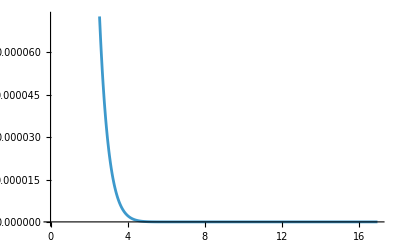

```mathematica
Plot[IsotropicCoordsPressure[rbar], {rbar, 0, rbarStar+10}]
```

### Sorting out the speed of sound as a function of r: a(r)

```mathematica
(*Getting the derivative of the density*)
rhodummy[r_] := rho0(1 - r/RStar)^6
rhodummy'[r];
drhodr[r_] := (-6 rho0)/RStar(1-r/RStar)^5
```

```mathematica
cutoff = .999RStar
```

7.992

#### Speed of sound in isotropic coordinates

```mathematica
cutoffIso = rbarofrInside[cutoff]
```

6.95606

```mathematica
(*Needed to implement these measures to speed things up using Module to avoid recomputation and also the N@ to return numbers instead of symbols for NDSolve, pressure was causing an issue*)
(*Module avoids repeating the calculation three times as there were three arguments I would have had to have inputted it in*)
```

```mathematica
asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]},Piecewise[{
{N@Sqrt[dPdr[r,Pressure[r]]/drhodr[r]],rbar<cutoffIso},{N@Sqrt[(M (RStar-r))/(6 RStar (RStar-2 M))],cutoffIso<=rbar<rbarStar},
{10^-6, rbar >= rbarStar}
}
]
]
```

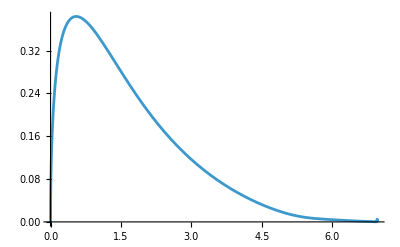

1/1000000

```mathematica
Plot[asosPiecewise[rbar], {rbar, 0, rbarStar}]
asosPiecewise[rbarStar]
```

## Setting up 2D ODEs for new density profile:

Constants that are going to be used

```mathematica
m = 10^-6; (*mass of PBH?*)
λGR[rbar_] := 1.49*asosPiecewise[rbar]
q = 2;
```

### Mach number interpolation

#### Interpolating

```mathematica
fMachLow[m_] := 1/2 Log[(1+ m)/(1 - m)] - m ;
fMachhigh[m_] := 1/2 Log[1 - 1/m^2]  + 10
```

```mathematica
x1=.98;
x2=1.02;
y1=fMachLow[x1];
y2=fMachhigh[x2];
```

```mathematica
anaylticline[Mach_] := y1 + (y2 - y1) (Mach - x1)/(x2 - x1)
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.98},
{anaylticline[Μach], 0.98 < Μach  < 1.02},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.02}
}];
```

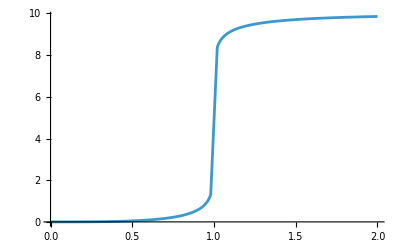

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, Exclusions->None, PlotRange->All]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
umagOutside[rbar_, ur_, uphi_]:=(√(ur^2+(uphi/rbar)^2))/A[rbar]
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;
```

Gravitational Waves

```mathematica
FRRr[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarOutside[rbar]},((8 m^2)/(15 r^4)*drBardt[rbar, ur, uphi]*(8 M^2+r M (6 drBardt[rbar, ur, uphi]^2+36 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
FRRphi[m_, rbar_,ur_, uphi_]:= Module[{r = rofrbarOutside[rbar]},((8 m^2)/(5 r^4)*dphidtOutside[rbar,ur, uphi]*(2 M^2+r M (9 drBardt[rbar, ur, uphi]^2-6 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
duphidtOutside[m_, rbar_, ur_, uphi_] := η/m(A[rbar]^2 rbar^2 FRRphi[m, rbar, ur, uphi]);

durdt2DOutside[m_, rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3)) + η/m(A[rbar]^2 FRRr[m, rbar, ur, uphi]);
```

```mathematica
(*η/m(A[rbar]^2 rbar^2 FRRphi[rbar, ur, uphi])
+ η/m(A[rbar]^2 FRRr[rbar, ur, uphi])*)
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagInside[rbar_, ur_, uphi_] := (√(ur^2+(uphi/rbar)^2))/AInside[rbar]
```

#### Mach business

```mathematica
Mach[rbar_, ur_, uphi_] :=((√(ur^2+(uphi/rbar)^2))/AInside[rbar])/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi])
```

#### Dissipative Forces

Accretion

```mathematica
(*q=2, Γ=2*)
mdot[m_, rbar_, ur_, uphi_] := 1.49* (4Pi rho0 m^2)/(asosPiecewise[rbar]^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2);
```

```mathematica
dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar] (1.49)(rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/(asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar] (1.49)(rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/(asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))uphi (*a's simplify in this regime*)
```

Drag

```mathematica
dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagInside[rbar, ur, uphi]^3(-4π αInside[rbar]*(rho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagInside[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagInside[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagInside[rbar, ur, uphi]^3;
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_, ur_, uphi_] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;
```

```mathematica
(*Redefining the mass function without the piecewise component for simplicity*)
MassFunction[r_] := 252(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3));
```

```mathematica
Mp[r_] := Derivative[1][MassFunction][r]
Mpp[r_] := Derivative[2][MassFunction][r]
Mppp[r_] := Derivative[3][MassFunction][r]
```

```mathematica
FRRrIns[m_, rbar_, ur_, uphi_]:= Module[{r = rofrbarInside[rbar]},(8 m^2)/(15 r^4)*drBardtInside[rbar, ur, uphi]*(8 MassFunction[r]^2+r MassFunction[r] (6 drBardtInside[rbar, ur, uphi]^2+36 r^2 dphidtInside[rbar, ur, uphi]^2+Mp[r]-3 r Mpp[r])-r^2 ( Mp[r]^2+3 r^2 dphidtInside[rbar, ur, uphi]^2 (6 Mp[r]-r Mpp[r])+drBardtInside[rbar, ur, uphi]^2 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))];
```

```mathematica
FRRphiIns[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarInside[rbar]},(8 m^2)/(5 r^4)*dphidtInside[rbar, ur, uphi]*(2 MassFunction[r]^2+2 r^4 dphidtInside[rbar, ur, uphi]^2 Mp[r]+r MassFunction[r] (9 drBardtInside[rbar, ur, uphi]^2-6 r^2 dphidtInside[rbar, ur, uphi]^2-2 Mp[r])-r^2 drBardtInside[rbar, ur, uphi]^2 (7 Mp[r]-2 r Mpp[r]))];
```

```mathematica
duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtaccretionphi[m, rbar, ur, uphi] + dpdtdragphi[m, rbar, ur, uphi] + AInside[rbar]^2 rbar^2 FRRphiIns[m, rbar, ur, uphi]);

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3))+ η/m(dpdtaccretionr[m, rbar, ur, uphi] + dpdtdragr[m, rbar, ur, uphi] + AInside[rbar]^2 FRRrIns[m, rbar, ur, uphi]);
```

```mathematica
(* + 0*AInside[rbar]^2 FRRrIns[rbar, ur, uphi]
 + 0*AInside[rbar]^2 rbar^2 FRRphiIns[rbar, ur, uphi]*)
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
(*eccentricity = 9/11; (*Obtained from setting periapsis to 5.5 and ptilde still to 10*)*)
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];

rperiapsis[eccentricity, ptilde]; (*Setting it up such that it passes the point where I know the accretion is strong enough to sufficiently slow it down from the inside simulation. (Needed this for accretion and drag to work independently and together, GW allowed me to go back to it not having to pass through the star on the first orbit) 
Used this to find the proper rapoapsis*)
```

```mathematica
(*r_a + r_p = 2a, a = p/(1-e^2) = 30.25
r_a = 60.5-5.5 = 55 = rbar0 = r_apoapsis*)
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
drBardtInside[rbarStar,0, AngularMomentumUphi0]
durdt2DInside[m, rbarStar,0, AngularMomentumUphi0]
duphidtInside[m, rbarStar,0, AngularMomentumUphi0]
dphidtInside[rbarStar,0, AngularMomentumUphi0]
```

0.

0.00219943

-5.4786×10^-9 η

0.0466817

```mathematica
t0=0;
tEnd=50000;
η = 7.25 10^3;

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->MachinePrecision (*Machine precision and 20k max steps also works*)
][[1]];
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

9552.67

159.819

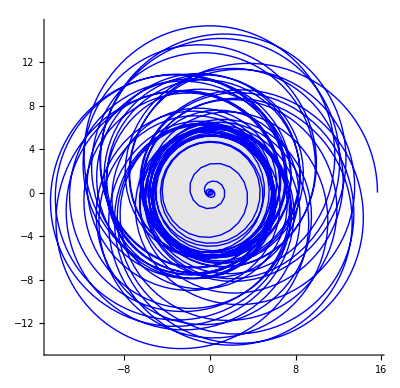

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

```mathematica
FRRrFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{FRRr[m, rbar, ur, uphi], rbar >= rbarStar},
{FRRrIns[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {9.46828} lies outside the range of data in the interpolating function. Extrapolation will be used.

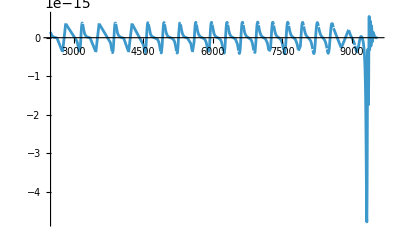

```mathematica
Plot[FRRrFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 2500, tFinish}, PlotRange->All]
```

```mathematica
FRRphiFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{FRRphi[m, rbar, ur, uphi], rbar >= rbarStar},
{FRRphiIns[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {9.46828} lies outside the range of data in the interpolating function. Extrapolation will be used.

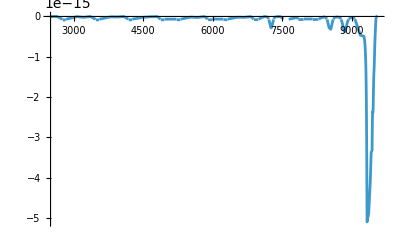

```mathematica
Plot[FRRphiFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 2500, tFinish}, PlotRange->All]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

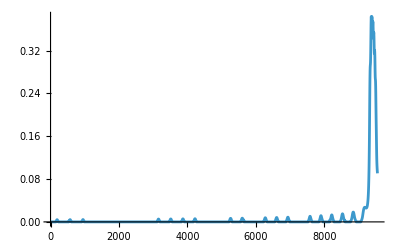

```mathematica
Plot[asosPiecewise[rbarNumIn[t]],{t,0,tFinish}, PlotRange->All]
```

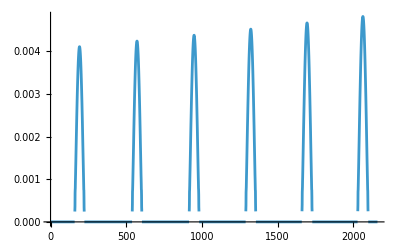

```mathematica
Plot[
{
Piecewise[
{
{0,rbarNumIn[t]>=rbarStar},
{asosPiecewise[rbarNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

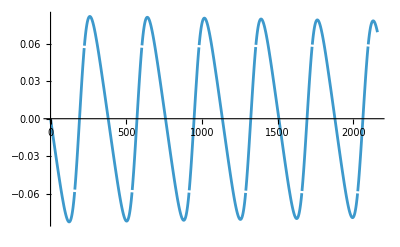

```mathematica
Plot[
{
Piecewise[
{
{drBardt[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{drBardtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

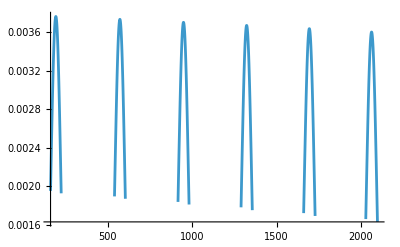

```mathematica
Plot[
{
Piecewise[
{
{durdt2DOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{durdt2DInside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

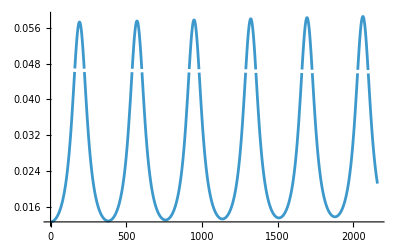

```mathematica
Plot[
{
Piecewise[
{
{dphidtOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{dphidtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

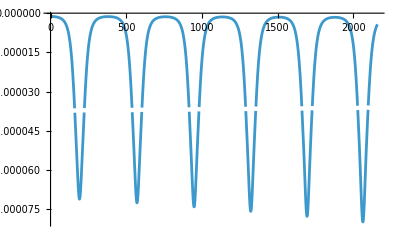

```mathematica
Plot[
{
Piecewise[
{
{duphidtOutside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]], rbarNumIn[t]>=rbarStar},
{duphidtInside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

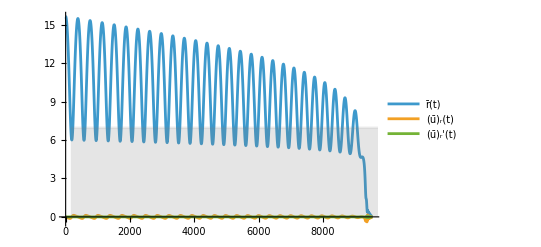

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

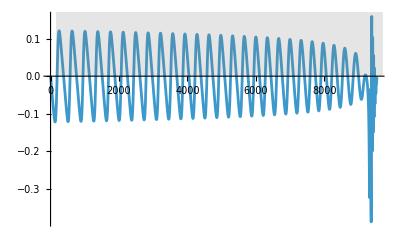

```mathematica
outFigRadial=Show[Plot[{urNumIn[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

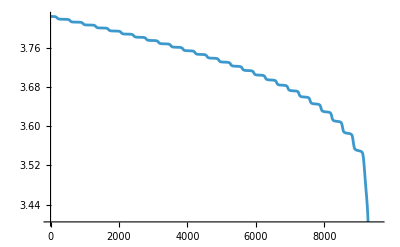

```mathematica
outFigAngular=Plot[{uphiNumIn[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

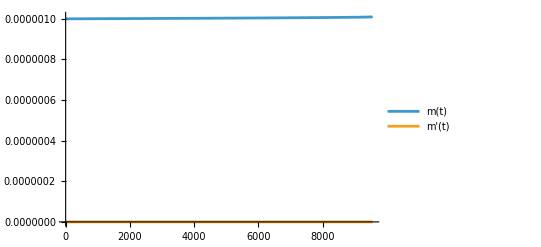

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn'[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]]]
```

```mathematica
umag[rbar_, ur_, uphi_] := Piecewise[
{
{umagOutside[rbar, ur, uphi], rbar >= rbarStar},
{umagInside[rbar, ur, uphi], rbar < rbarStar}
}
]
```

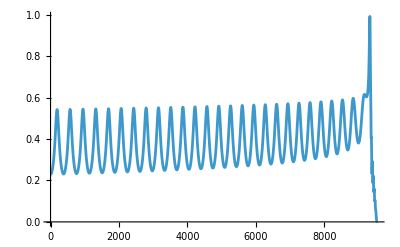

```mathematica
Plot[umag[rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, Exclusions->None] (*Normal behaviour judging from rho=const simulation*)
```

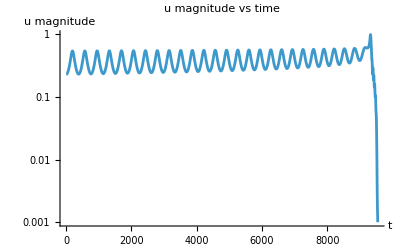

```mathematica
LogPlot[Evaluate[umag[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
```

```mathematica
(*Show me the value of u at tfinish*)
umag[rbarNumIn[tFinish],urNumIn[tFinish],uphiNumIn[tFinish]]/. solIn
```

0.000995684